## Computations

### Î(p,n)

```mathematica
hatI[p_,ν_]:= (Sqrt[π](2p)!)/(2^(2p)p!)*Gamma[(ν-2)/2]/(Gamma[(ν-1)/2+p]);
```

#### Checks

```mathematica
nHatI[p_,ν_]:=NIntegrate[Sin[t]^(ν-3)*Cos[t]^(2p),{t,0,π}]
Module[{ps,ns,analy, num},
ps={0,1,2,3,4,5,10};
ns={3.9,4,4.1,4.01,π,5};
analy=Table[Table[hatI[p,n],{n,ns}],{p,ps}];
Print@analy;
Print@N@analy;
num=Table[Table[nHatI[p,n],{n,ns}],{p,ps}];
Print@num;
Print@(N@analy-num)
]
```

{{2.06422,2,1.94122,1.99389,(√π Gamma[1/2 (-2+π)])/Gamma[1/2 (-1+π)],π/2},{0.711801,2/3,0.626201,0.662422,(√π Gamma[1/2 (-2+π)])/(2 Gamma[1+1/2 (-1+π)]),π/8},{0.435797,2/5,0.368353,0.39666,(3 √π Gamma[1/2 (-2+π)])/(4 Gamma[2+1/2 (-1+π)]),π/16},{0.315795,2/7,0.259404,0.282924,(15 √π Gamma[1/2 (-2+π)])/(8 Gamma[3+1/2 (-1+π)]),(5 π)/128},{0.248378,2/9,0.199541,0.219808,(105 √π Gamma[1/2 (-2+π)])/(16 Gamma[4+1/2 (-1+π)]),(7 π)/256},{0.205083,2/11,0.16179,0.17968,(945 √π Gamma[1/2 (-2+π)])/(32 Gamma[5+1/2 (-1+π)]),(21 π)/1024},{0.110736,2/21,0.0822285,0.0938335,(654729075 √π Gamma[1/2 (-2+π)])/(1024 Gamma[10+1/2 (-1+π)]),(4199 π)/524288}}

{{2.06422,2.,1.94122,1.99389,2.86928,1.5708},{0.711801,0.666667,0.626201,0.662422,1.33979,0.392699},{0.435797,0.4,0.368353,0.39666,0.970488,0.19635},{0.315795,0.285714,0.259404,0.282924,0.790095,0.122718},{0.248378,0.222222,0.199541,0.219808,0.67931,0.0859029},{0.205083,0.181818,0.16179,0.17968,0.602843,0.0644272},{0.110736,0.0952381,0.0822285,0.0938335,0.412425,0.0251609}}

{{2.06422,2.,1.94122,1.99389,2.86928,1.5708},{0.711801,0.666667,0.626201,0.662422,1.33979,0.392699},{0.435797,0.4,0.368353,0.39666,0.970488,0.19635},{0.315795,0.285714,0.259404,0.282924,0.790095,0.122718},{0.248378,0.222222,0.199541,0.219808,0.67931,0.0859029},{0.205083,0.181818,0.16179,0.17968,0.602843,0.0644272},{0.110736,0.0952381,0.0822285,0.0938335,0.412425,0.0251609}}

{{-4.21939×10^-8,-8.88178×10^-16,1.8722×10^-8,1.50629×10^-8,-2.75335×10^-14,-1.77636×10^-15},{-1.23124×10^-13,-4.44089×10^-16,-8.60423×10^-14,9.40151×10^-9,-1.33227×10^-15,-4.44089×10^-16},{-6.66134×10^-16,-3.33067×10^-16,-1.72196×10^-13,3.73975×10^-9,-5.55112×10^-16,-2.22045×10^-16},{-4.44089×10^-16,-2.77556×10^-16,-3.33067×10^-16,1.86989×10^-9,-3.33067×10^-16,-1.52656×10^-16},{-2.30371×10^-15,-2.13718×10^-15,-1.47105×10^-15,3.7398×10^-9,-1.11022×10^-15,-4.8711×10^-15},{-3.33067×10^-16,-1.66533×10^-16,-2.22045×10^-16,1.86991×10^-9,3.88578×10^-15,-8.32667×10^-17},{3.30208×10^-13,3.32276×10^-13,3.33039×10^-13,3.3272×10^-13,2.7045×10^-13,-3.46945×10^-18}}

#### comments

```mathematica
Module[{f,g},
f[p_,n_]=π/(2^(2p+n-3)(n-2))*Sum[Binomial[2p,k]Exp[I π(k-p)]/Beta[(n-1)/2+(k-p),(n-1)/2-(k-p)],{k,0,2p}];
Print[FullSimplify[f[0,n]-hatI[0,n]]];
Print[f[1,n]];
Print[hatI[1,n]];
Print[FullSimplify[f[1,n]]];
Print[FullSimplify[hatI[1,n]]];
Print[FullSimplify[f[1,n]-hatI[1,n]]];
Print[];
Print[f[2,n]];
Print[FullSimplify[f[2,n]]];
Print[FullSimplify[hatI[2,n]]];
Print[FullSimplify[f[2,n]-hatI[2,n]]];
Print[];
Print[FullSimplify[f[3,n]-hatI[3,n]]];
Print[FullSimplify[f[4,n]-hatI[4,n]]];
]
```

0

(2^(3-n) π Gamma[-1+n])/((-3+n) (-2+n) Gamma[1/2 (-3+n)] Gamma[(1+n)/2])

(√π Gamma[1/2 (-2+n)])/(2 Gamma[1+1/2 (-1+n)])

(√π Gamma[-1+n/2])/(2 Gamma[(1+n)/2])

(√π Gamma[-1+n/2])/(2 Gamma[(1+n)/2])

0

(3 2^(3-n) π Gamma[-1+n])/((-5+n) (-3+n) (-2+n) Gamma[1/2 (-5+n)] Gamma[(3+n)/2])

(3 √π Gamma[-1+n/2])/(4 Gamma[(3+n)/2])

(3 √π Gamma[-1+n/2])/(4 Gamma[(3+n)/2])

0

0

0

```mathematica
Module[{a,n},
(*a=(3*1*(-1)/((3!)^2)-2*3*(-3)/4!/2!+2*3*(-5)*(-3)/5!-2/6!(-3)(-5)(-7))*6!;
Print@a;
Print@FactorInteger[a];


a=(
(5*3*1*(-1))/((4!)^2)-2/5!/3!*(5*3*1)((-3))+2/6!/2!(5*3)((-3)(-5))-2/7!/1!(5)((-3)(-5)(-7))+2/8!/0!*((-3)(-5)(-7)(-9))
)*8!;
Print@a;
Print@FactorInteger[a];*)

n[p_]:=(Sow[1/((p!)^2)Pochhammer[-1/2,p],"0"]
+2Sum[
Sow[(-1)^(l)/((p+l)!(p-l)!),"l"]
*Sow[(Pochhammer[-1/2+l,p-l]),"a"]
*Sow[( Pochhammer[-1/2-l,l]),"b"],
{l,p}])*(p)!(*/2^(p)*);
Print@Reap@n[0];
Print@Reap@n[1];
Print@FactorInteger@n[2];
Print@FactorInteger@n[3];
Print@FactorInteger@n[4];
Print@FactorInteger@n[5];
Print@FactorInteger@n[6];
]
```

{1,{{1}}}

{1,{{-1/2},{-1/2},{1},{-3/2}}}

{{1,1}}

{{1,1}}

{{1,1}}

«2 more identical outputs»

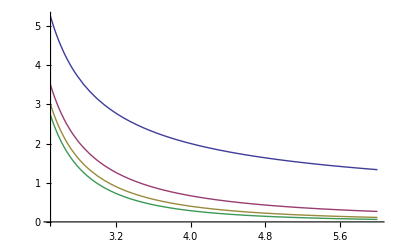

```mathematica
Plot[Evaluate[Table[hatI[p,n],{p,0,3}]],{n,2.5,6}]
```

### any collinearity -k,-l ∈ Ν_0

```mathematica
FullSimplify[hatI[0,n-1]*hatI[0,n]]
```

(2 π)/(-3+n)

```mathematica
FullSimplify[(a^2hatI[0,n]+b^2 hatI[1,n])*hatI[0,n-1]]
```

(2 (b^2+a^2 (-1+n)) π)/((-3+n) (-1+n))

```mathematica
FullSimplify[(A^2hatI[0,n]+B^2 hatI[1,n])*hatI[0,n-1] + C^2 hatI[1,n-1]hatI[0,n+2]]
```

(2 (B^2+C^2+A^2 (-1+n)) π)/((-3+n) (-1+n))

```mathematica
FullSimplify[(a A hatI[0,n]+b B hatI[1,n])*hatI[0,n-1]]
```

(2 (b B+a A (-1+n)) π)/((-3+n) (-1+n))

### collinear a

#### Check to hep-ph 0005120 and Phys.Rev.D40.54

```mathematica
FullSimplify[hatI[0,n-1]*hatI[0,n-2]]
```

(2 π)/(-4+n)

```mathematica
Module[{a},
a=hatI[0,n-1]*(A hatI[0,n-2]+B hatI[1,n-2]);
a=FullSimplify[a];
Print@a;
Print@FullSimplify[a-2π(A(n-3)+B)/((n-3)(n-4))];
Print@FullSimplify@Series[a/.{n-> 4+ϵ},{ϵ,0,0}]
]
```

(2 (B+A (-3+n)) π Gamma[-4+n])/Gamma[-2+n]

0

(2 (A+B) π)/ϵ-2 (B π)+O[ϵ]^1

```mathematica
2π(A(n-3)+B)/((n-3)(n-4))
```

(2 (B+A (-3+n)) π)/((-4+n) (-3+n))

```mathematica
Module[{a},
a=hatI[0,n-1]*(A^2 hatI[0,n-2]+(B^2+2A B) hatI[1,n-2])+C^2hatI[1,n-1] hatI[0,n];
a=FullSimplify[a];
Print@a;
Print@FullSimplify[a-2π((A+B)^2/(n-4)-(B^2+2A B-C^2)/(n-3)-C^2/(n-2))];
Print@Series[a/.{n-> 4+ϵ},{ϵ,0,0}]
]
```

(2 (C^2 (-4+n)+(2 A B+B^2+A^2 (-3+n)) (-2+n)) π)/((-4+n) (-3+n) (-2+n))

0

(2 A^2 π+4 A B π+2 B^2 π)/ϵ+(-4 A B π-2 B^2 π+C^2 π)+O[ϵ]^1

```mathematica
FullSimplify[hatI[0,n-1]*(hatI[0,n-4]+hatI[1,n-4])]
```

(2 π)/(-6+n)

```mathematica
Module[{a},
a=hatI[0,n-1]*(A (hatI[0,n-4]+hatI[1,n-4])+2B hatI[1,n-4]);
a=FullSimplify[a];
Print@a;
Print@FullSimplify[a-(*2π(A(n-3)+B)/((n-3)(n-4))*)0];
Print@FullSimplify@Series[a/.{n-> 4+ϵ},{ϵ,0,0}]
]
```

(2 (2 B+A (-4+n)) π)/((-6+n) (-4+n))

(2 (2 B+A (-4+n)) π)/((-6+n) (-4+n))

-(2 (B π))/ϵ-(A+B) π+O[ϵ]^1

```mathematica
Module[{a},
a=hatI[0,n-1]*(A^2 (hatI[0,n-4]+hatI[1,n-4])+4A B hatI[1,n-4]+B^2(hatI[1,n-4]+hatI[2,n-4]))+C^2hatI[1,n-1]( hatI[0,n-2]+hatI[1,n-2]);
a=FullSimplify[a];
Print@a;
Print@FullSimplify[a-2π((A+B)^2/(n-6)+(C^2-2B(A+B))/(n-4)+(B^2-C^2)/(n-3))];
Print@Series[a/.{n-> 4+ϵ},{ϵ,0,1}]
]
```

(2 (C^2 (-6+n)+4 A B (-3+n)+A^2 (-4+n) (-3+n)+B^2 n) π)/((-6+n) (-4+n) (-3+n))

0

(-4 A B π-4 B^2 π+2 C^2 π)/ϵ+(-A^2 π-2 A B π+B^2 π-2 C^2 π)+(-(A^2 π)/2-A B π-(5 B^2 π)/2+2 C^2 π) ϵ+O[ϵ]^2

```mathematica
Module[{f},
f = B/(A+B) (Sin[t1]^(n-3) Sin[t2]^(n-4))/(A+B Cos[t1] + C Sin[t1] Cos[t2])-C/(A+B) (Sin[t1]^(n-4) Sin[t2]^(n-4)(1+Cos[t1])Cos[t2])/(A+B Cos[t1] + C Sin[t1] Cos[t2]);
Print@f;
Print@Series[f/.{n-> 4+ϵ},{ϵ,0,2}]
]
```

-(C (1+Cos[t1]) Cos[t2] Sin[t1]^(-4+n) Sin[t2]^(-4+n))/((A+B) (A+B Cos[t1]+C Cos[t2] Sin[t1]))+(B Sin[t1]^(-3+n) Sin[t2]^(-4+n))/((A+B) (A+B Cos[t1]+C Cos[t2] Sin[t1]))

(-C Cos[t2]-C Cos[t1] Cos[t2]+B Sin[t1])/((A+B) (A+B Cos[t1]+C Cos[t2] Sin[t1]))+(-(C (1+Cos[t1]) Cos[t2] (Log[Sin[t1]]+Log[Sin[t2]]))/((A+B) (A+B Cos[t1]+C Cos[t2] Sin[t1]))+(B (Log[Sin[t1]] Sin[t1]+Log[Sin[t2]] Sin[t1]))/((A+B) (A+B Cos[t1]+C Cos[t2] Sin[t1]))) ϵ+(-(C (1+Cos[t1]) Cos[t2] (Log[Sin[t1]]^2+2 Log[Sin[t1]] Log[Sin[t2]]+Log[Sin[t2]]^2))/(2 (A+B) (A+B Cos[t1]+C Cos[t2] Sin[t1]))+(B (Log[Sin[t1]]^2 Sin[t1]+2 Log[Sin[t1]] Log[Sin[t2]] Sin[t1]+Log[Sin[t2]]^2 Sin[t1]))/(2 (A+B) (A+B Cos[t1]+C Cos[t2] Sin[t1]))) ϵ^2+O[ϵ]^3

```mathematica
FullSimplify@Integrate[Cos[t2]/(A+B Cos[t1]+C Cos[t2] Sin[t1]),t2]
```

((t2-(2 √2 ArcTan[(√2 (A+B Cos[t1]-C Sin[t1]) Tan[t2/2])/(√(2 A^2+B^2-C^2+4 A B Cos[t1]+(B^2+C^2) Cos[2 t1]))] (A+B Cos[t1]))/(√(2 A^2+B^2-C^2+4 A B Cos[t1]+(B^2+C^2) Cos[2 t1]))) Csc[t1])/C

```mathematica
Integrate[(-C Cos[t2]-C Cos[t1] Cos[t2]+B Sin[t1])/(A+B Cos[t1]+C Cos[t2] Sin[t1]),t1]
Integrate[(-C Cos[t2]-C Cos[t1] Cos[t2]+B Sin[t1])/(A+B Cos[t1]+C Cos[t2] Sin[t1]),t2]
```

(-2 √2 C ArcTanh[(2 (B-ⅈ C Cos[t2]) Sec[t1/2] (C Cos[t1/2] Cos[t2]+(A-B) Sin[t1/2]))/(√(-(B-ⅈ C Cos[t2])^2) √(4 A^2-4 B^2-2 C^2-2 C^2 Cos[2 t2]))] Cos[t2] √((ⅈ B+C Cos[t2])^2)-(B-ⅈ C Cos[t2]) √(2 A^2-2 B^2-C^2-C^2 Cos[2 t2]) Log[2 (A+B Cos[t1]+C Cos[t2] Sin[t1])])/((B-ⅈ C Cos[t2]) √(2 A^2-2 B^2-C^2-C^2 Cos[2 t2]))

(-t2+(2 √2 (A+B) ArcTan[(√2 (A+B Cos[t1]-C Sin[t1]) Tan[t2/2])/(√(2 A^2+B^2-C^2+4 A B Cos[t1]+(B^2+C^2) Cos[2 t1]))])/(√(2 A^2+B^2-C^2+4 A B Cos[t1]+(B^2+C^2) Cos[2 t1]))) Cot[t1/2]

```mathematica
Module[{as,f,g,h,k},
k[t1_,t2_]=(B Sin[t1]-C Cos[t2](1+Cos[t1]))/((A+B Cos[t1]+C Sin[t1] Cos[t2])(A+B));
Print@Series[k[t1,t2],{t1,0,2},{t2,0,2}];
as={A∈Reals,B∈Reals,C∈Reals,A+B≠ 0};
f[t1_,t2_]=FullSimplify@Integrate[k[t1,t2],t2,Assumptions-> as];
Print@f[t1,t2];
Print@f[t1,0];
g[t1_]=FullSimplify@Limit[f[t1,t2],t2-> π,Assumptions-> as];
Print@g[t1];
Print@Series[g[t1],{t1,0,2}];
Print@Series[g[t1],{t1,2π,2}];
h[t1_]=FullSimplify@Integrate[g[t1],t1,Assumptions->as];
Print@h[t1];
Print@Series[h[t1],{t1,0,1},Assumptions->as];
Print@Limit[h[t1],t1-> 0,Assumptions->as];
Print@FullSimplify@Limit[h[t1],t1-> π,Assumptions->as];
]
```

(-(2 C)/(A+B)^2+(C t2^2)/(A+B)^2+O[t2]^3)+((B/(A+B)^2+(2 C^2)/(A+B)^3)-(2 C^2 t2^2)/(A+B)^3+O[t2]^3) t1+((-(2 B C)/(A+B)^3+C/(2 (A+B)^2)-(2 C^3)/(A+B)^4)+((B C)/(A+B)^3-C/(4 (A+B)^2)+(3 C^3)/(A+B)^4) t2^2+O[t2]^3) t1^2+O[t1]^3

((-t2+(2 √2 (A+B) ArcTan[(√2 (A+B Cos[t1]-C Sin[t1]) Tan[t2/2])/(√(2 A^2+B^2-C^2+4 A B Cos[t1]+(B^2+C^2) Cos[2 t1]))])/(√(2 A^2+B^2-C^2+4 A B Cos[t1]+(B^2+C^2) Cos[2 t1]))) Cot[t1/2])/(A+B)

0

π Cot[t1/2] (-1/(A+B)-1/((A+B Cos[t1]+C Sin[t1]) √(1-(2 C Sin[t1])/(A+B Cos[t1]+C Sin[t1]))))

-(4 π)/((A+B) t1)+((A^2-A B-2 B^2-3 C^2) π t1)/(3 (A+B)^3)+O[t1]^3

-(4 π)/((A+B) (t1-2 π))+((A^2-A B-2 B^2-3 C^2) π (t1-2 π))/(3 (A+B)^3)+O[t1-2 π]^3

π (-(2 Log[Sin[t1/2]])/(A+B)+(Cos[t1/2]^2 (-Log[Tan[t1/2]^2]+Log[(A+B) (A+B+(√((2 A^2+B^2-C^2+4 A B Cos[t1]+(B^2+C^2) Cos[2 t1]) Sec[t1/2]^4))/(√2))+(A^2-B^2-2 C^2) Tan[t1/2]^2]) √((2 A^2+B^2-C^2+4 A B Cos[t1]+(B^2+C^2) Cos[2 t1]) Sec[t1/2]^4))/((A+B) (A+B Cos[t1]+C Sin[t1]) √(2-(4 C Sin[t1])/(A+B Cos[t1]+C Sin[t1]))))

π ((√((A+B)^2) (Log[4]+Log[(A+B) (A+B+√((A+B)^2))]-2 Log[t1]))/(A+B)^2+(2 (Log[2]-Log[t1]))/(A+B))+O[t1]^2

DirectedInfinity[A+B+Abs[A+B]]

(π Abs[A-B] Log[A^2-B^2-2 C^2+(A+B) Abs[A-B]])/((A-B) (A+B))

```mathematica
FullSimplify[1/(A+B Cos[t1]+C Sin[t1] Cos[t2]) - ((B(1-Cos[t1])-C Sin[t1]Cos[t2])/(A+B Cos[t1]+C Sin[t1] Cos[t2])/(A+B)+1/(A+B))]
Together[1/(A+B Cos[t1]+C Sin[t1] Cos[t2]) - 1/(A+B)]
FullSimplify[Sin[t1]/(1-Cos[t1])/(A+B Cos[t1]+C Sin[t1] Cos[t2])-((B Sin[t1]-C Cos[t2](1+Cos[t1]))/((A+B Cos[t1]+C Sin[t1] Cos[t2])(A+B))+Sin[t1]/(A+B)/(1-Cos[t1]))]
```

0

(B-B Cos[t1]-C Cos[t2] Sin[t1])/((A+B) (A+B Cos[t1]+C Cos[t2] Sin[t1]))

0

```mathematica
Module[{as,k,K1,uK1,lK1,k1},
as={A∈Reals,B∈Reals,C∈Reals,A>B,A+B≠ 0,A^2 ≠ B^2+C^2};
k[t1_,t2_,n_]=Sin[t1]^(n-4)Sin[t2]^(n-4)/(A+B Cos[t1]+C Sin[t1] Cos[t2])*(B Sin[t1]-C Cos[t2](1+Cos[t1]));
(*Print@Integrate[k[t1,t2,4],t2];*)
K1[t1_,t2_]=FullSimplify@Integrate[k[t1,t2,4],t1,Assumptions-> as];
Print@K1[t1,t2];
uK1[t2_]=FullSimplify@Limit[K1[t1,t2],t1-> π,Assumptions-> as];
lK1[t2_]=FullSimplify@Limit[K1[t1,t2],t1-> 0,Assumptions-> as];
Print@{uK1[t2],lK1[t2]};
k1[t2_]=FullSimplify[uK1[t2]-lK1[t2],Assumptions-> as];
Print@k1[t2];
Print@Integrate[k1[t2],t2,Assumptions-> as];
]
```

-(2 C ArcTan[(C Cos[t2]+(A-B) Tan[t1/2])/(√(A^2-B^2-C^2/2-1/2 C^2 Cos[2 t2]))] Cos[t2])/(√(A^2-B^2-C^2/2-1/2 C^2 Cos[2 t2]))-Log[2 (A+B Cos[t1]+C Cos[t2] Sin[t1])]

{√2 C π Cos[t2] √(-1/(-2 A^2+2 B^2+C^2+C^2 Cos[2 t2]))-Log[2 (A-B)],-(2 C ArcTan[(C Cos[t2])/(√(A^2-B^2-C^2/2-1/2 C^2 Cos[2 t2]))] Cos[t2])/(√(A^2-B^2-C^2/2-1/2 C^2 Cos[2 t2]))-Log[2 (A+B)]}

√2 C Cos[t2] ((2 ArcTan[(C Cos[t2])/(√(A^2-B^2-C^2/2-1/2 C^2 Cos[2 t2]))])/(√(2 A^2-2 B^2-C^2-C^2 Cos[2 t2]))+π √(-1/(-2 A^2+2 B^2+C^2+C^2 Cos[2 t2])))+Log[1/(A-B)]+Log[A+B]

Integrate[√2 C Cos[t2] ((2 ArcTan[(C Cos[t2])/(√(A^2-B^2-C^2/2-1/2 C^2 Cos[2 t2]))])/(√(2 A^2-2 B^2-C^2-C^2 Cos[2 t2]))+π √(-1/(-2 A^2+2 B^2+C^2+C^2 Cos[2 t2])))+Log[1/(A-B)]+Log[A+B],t2,Assumptions→{A∈Reals,B∈Reals,C∈Reals,A>B,A+B≠0,A^2≠B^2+C^2}]

```mathematica
Integrate[Cos@t/(αβ+γ Cos@t),t]
Integrate[Cos@t/(αβ+γ Cos@t),{t,0,π}]
```

(t+(2 αβ ArcTanh[((αβ-γ) Tan[t/2])/(√(-αβ^2+γ^2))])/(√(-αβ^2+γ^2)))/γ

ConditionalExpression[(π (γ+αβ (-1+√((αβ-γ)/(αβ+γ)))))/(γ (-αβ+γ)),(αβ/γ∉Reals||Re[αβ/γ]≥1||Re[αβ/γ]≤-1)&&αβ≠γ&&αβ+γ≠0]

```mathematica
Hypergeometric2F1[1,3/2,2,z]
```

-(2 (-1+√(1-z)))/(√(1-z) z)

```mathematica
Beta[3/2,1/2]
```

π/2

```mathematica
Integrate[q/(Sqrt[2(A^2-B^2)-q^2]Sqrt[2C^2-q^2]),q]
FullSimplify[D[2ArcTan[Sqrt[2]q/Sqrt[(2(A^2-B^2)-q^2)]],q],Assumptions-> {A∈Reals,B∈Reals,A^2≠B^2+C^2,Sqrt[2]C≥ q≥ -Sqrt[2]C}]
```

-Log[√(2 A^2-2 B^2-q^2)+√(2 C^2-q^2)]

(4 (A-B) (A+B))/(√(A^2-B^2-q^2/2) (2 A^2-2 B^2+q^2))

```mathematica
Integrate[q/(Sqrt[2(A^2-B^2)-q^2]Sqrt[2C^2-q^2])*(2ArcTan[q/Sqrt[(2(A^2-B^2)-q^2)]]+π),q]
```

∫(q (π+2 ArcTan[q^2/(2 (A^2+B^2)-q^2)]))/(√(2 (A^2+B^2)-q^2) √(2 C^2-q^2))ⅆq

```mathematica
Integrate[Log[√(2 (A^2- B^2)-q^2)+√(2 C^2-q^2)]*((4 (A-B) (A+B))/(√(A^2-B^2-q^2/2) (2 A^2-2 B^2+q^2))),{q,-γ,γ},Assumptions-> {A∈Reals,B∈Reals,C∈Reals,A>B,A+B≠ 0,A^2 ≠ B^2+C^2}]
```

Integrate[(4 (A-B) (A+B) Log[√(2 (A^2-B^2)-q^2)+√(2 C^2-q^2)])/(√(A^2-B^2-q^2/2) (2 A^2-2 B^2+q^2)),{q,-γ,γ},Assumptions→{A∈Reals,B∈Reals,C∈Reals,A>B,A+B≠0,A^2≠B^2+C^2}]

```mathematica
Integrate[π q/Sqrt[2(A^2-B^2)-q^2]/Sqrt[2C^2-q^2],{q,-γ,γ}]
```

0

```mathematica
FullSimplify@Integrate[q/(Sqrt[A^2-B^2-q^2]Sqrt[C^2-q^2]),q]
FullSimplify[D[ArcTan[Sqrt[2]q/Sqrt[A^2-B^2-q^2]],q],Assumptions-> {A∈Reals,B∈Reals,A^2≠B^2+C^2,Sqrt[2]C≥ q≥ -Sqrt[2]C}]
```

1/2 Log[-A^2+B^2-C^2+2 q^2+2 √(A^2-B^2-q^2) √(C^2-q^2)]

(√2 (A-B) (A+B))/(√(A^2-B^2-q^2) (A^2-B^2+q^2))

```mathematica
FullSimplify@D[Log[( √(A^2-B^2-q^2)-√(C^2-q^2))^4],q]
FullSimplify@D[Log[( √(A^2-B^2-q^2)-√(C^2-q^2))],q]
```

(4 q)/(√((C-q) (C+q)) √(A^2-B^2-q^2))

q/(√((C-q) (C+q)) √(A^2-B^2-q^2))

```mathematica
-Sqrt[2]Integrate[Log[ √(A^2-B^2-q^2)-√(C^2-q^2)](A^2-B^2)/(Sqrt[A^2-B^2-q^2](A^2-B^2+q^2)),{q,0,C}]
```

$Aborted

```mathematica
Integrate[Log[p-Sqrt[γ-αβ+p^2]]/(2(αβ)-p^2)/Sqrt[αβ-p^2],p]
```

∫Log[p-√(p^2-αβ+γ)]/(√(-p^2+αβ) (-p^2+2 αβ))ⅆp

```mathematica
Integrate[1/(2(αβ)-p^2)/Sqrt[αβ-p^2],p]
D[1/(2(αβ)-p^2)/Sqrt[αβ-p^2],p]
```

ArcTan[p/(√2 √(-p^2+αβ))]/(√2 αβ)

(2 p)/(√(-p^2+αβ) (-p^2+2 αβ)^2)+p/((-p^2+αβ)^(3/2) (-p^2+2 αβ))

```mathematica
FullSimplify@Integrate[1/(A+B Cos[t1]+C Sin[t1] Cos [t2]),t1]
FullSimplify@Integrate[1/(A+B Cos[t1]+C Sin[t1] Cos [t2]),t2]
```

(2 ArcTan[(C Cos[t2]+(A-B) Tan[t1/2])/(√(A^2-B^2-C^2/2-1/2 C^2 Cos[2 t2]))])/(√(A^2-B^2-C^2/2-1/2 C^2 Cos[2 t2]))

(2 √2 ArcTan[(√2 (A+B Cos[t1]-C Sin[t1]) Tan[t2/2])/(√(2 A^2+B^2-C^2+4 A B Cos[t1]+(B^2+C^2) Cos[2 t1]))])/(√(2 A^2+B^2-C^2+4 A B Cos[t1]+(B^2+C^2) Cos[2 t1]))

```mathematica
Integrate[(B Sin[t1]-C Cos[t2](1+Cos[t1]))/((A+B Cos[t1]+C Sin[t1] Cos[t2])(A+B)),{t1,0,π},{t2,0,π},Assumptions->{A∈Reals,B∈Reals,C∈Reals,A>B,A+B≠ 0,A^2 ≠ B^2+C^2} ]
```

$Aborted

```mathematica
Module[{k,k2,symK2,i1,i2,j1,j2,i21},
k[t1_,t2_]=(B Sin[t1]-C Cos[t2](1+Cos[t1]))/((A+B Cos[t1]+C Sin[t1] Cos[t2])(A+B));
Print@FullSimplify[k[t1-π/2,t2-π/2]];
k2[t1_,t2_]=k[t1-π/2,t2-π/2];
symK2[t1_,t2_]=k2[t1,t2]+k2[t1,-t2];
Print@Factor@FullSimplify[symK2[t1,t2]];
i1[t1_,t2_]=FullSimplify@Integrate[symK2[t1,t2],t1,Assumptions->{A∈Reals,B∈Reals,C∈Reals,A>B,A+B≠ 0,A^2 ≠ B^2+C^2} ];
Print@i1[t1,t2];
Print@Limit[i1[t1,t2],t1-> -π/2];
Print@Limit[i1[t1,t2],t1-> π/2];
j1[t2_]=FullSimplify[Limit[i1[t1,t2],t1-> π/2]-Limit[i1[t1,t2],t1-> -π/2]];
Print@j1[t2];
Print@Integrate[j1[t2],t2,Assumptions->{A∈Reals,B∈Reals,C∈Reals,A>B,A+B≠ 0,A^2 ≠ B^2+C^2}];
(*i2[t1_,t2_]=FullSimplify@Integrate[k2[t1,t2]+k2[t1,-t2],t2];
Print@Limit[i2[t1,t2],t2-> 0];
j2[t1_]=FullSimplify@Limit[i2[t1,t2],t2-> π/2];
Print@j2[t1];
i21[t1_]=FullSimplify@Integrate[j2[t1],t1];
Print@Limit[i[t2],t2-> -π/2];
Print@Limit[i[t2],t2-> π/2];*)
]
```

-(B Cos[t1]+C (1+Sin[t1]) Sin[t2])/((A+B) (A+B Sin[t1]-C Cos[t1] Sin[t2]))

-(2 Cos[t1] (A B+B^2 Sin[t1]+C^2 Sin[t2]^2+C^2 Sin[t1] Sin[t2]^2))/((A+B) (A+B Sin[t1]-C Cos[t1] Sin[t2]) (A+B Sin[t1]+C Cos[t1] Sin[t2]))

(-√(2 A^2-2 B^2-C^2+C^2 Cos[2 t2]) (Log[A+B Sin[t1]-C Cos[t1] Sin[t2]]+Log[4 (A+B Sin[t1]+C Cos[t1] Sin[t2])])+2 √2 C (ArcTan[(B+(A-C Sin[t2]) Tan[t1/2])/(√(A^2-B^2-C^2/2+1/2 C^2 Cos[2 t2]))]-ArcTan[(B+(A+C Sin[t2]) Tan[t1/2])/(√(A^2-B^2-C^2/2+1/2 C^2 Cos[2 t2]))]) Sin[t2])/((A+B) √(2 A^2-2 B^2-C^2+C^2 Cos[2 t2]))

(-√(2 A^2-2 B^2-C^2+C^2 Cos[2 t2]) (Log[4]+2 Log[A-B])+2 √2 C ArcTan[(A-B+C Sin[t2])/(√(A^2-B^2-C^2/2+1/2 C^2 Cos[2 t2]))] Sin[t2]+2 √2 C ArcTan[(-A+B+C Sin[t2])/(√(A^2-B^2-C^2/2+1/2 C^2 Cos[2 t2]))] Sin[t2])/((A+B) √(2 A^2-2 B^2-C^2+C^2 Cos[2 t2]))

(-√(2 A^2-2 B^2-C^2+C^2 Cos[2 t2]) (Log[4]+2 Log[A+B])+2 √2 C ArcTan[(A+B-C Sin[t2])/(√(A^2-B^2-C^2/2+1/2 C^2 Cos[2 t2]))] Sin[t2]-2 √2 C ArcTan[(A+B+C Sin[t2])/(√(A^2-B^2-C^2/2+1/2 C^2 Cos[2 t2]))] Sin[t2])/((A+B) √(2 A^2-2 B^2-C^2+C^2 Cos[2 t2]))

(2 (√(2 A^2-2 B^2-C^2+C^2 Cos[2 t2]) (Log[A-B]-Log[A+B])+√2 C (ArcTan[(A-B-C Sin[t2])/(√(A^2-B^2-C^2/2+1/2 C^2 Cos[2 t2]))]+ArcTan[(A+B-C Sin[t2])/(√(A^2-B^2-C^2/2+1/2 C^2 Cos[2 t2]))]-ArcTan[(A-B+C Sin[t2])/(√(A^2-B^2-C^2/2+1/2 C^2 Cos[2 t2]))]-ArcTan[(A+B+C Sin[t2])/(√(A^2-B^2-C^2/2+1/2 C^2 Cos[2 t2]))]) Sin[t2]))/((A+B) √(2 A^2-2 B^2-C^2+C^2 Cos[2 t2]))

1/(A+B)2 Integrate[(√(2 A^2-2 B^2-C^2+C^2 Cos[2 t2]) (Log[A-B]-Log[A+B])+√2 C (ArcTan[(A-B-C Sin[t2])/(√(A^2-B^2-C^2/2+1/2 C^2 Cos[2 t2]))]+ArcTan[(A+B-C Sin[t2])/(√(A^2-B^2-C^2/2+1/2 C^2 Cos[2 t2]))]-ArcTan[(A-B+C Sin[t2])/(√(A^2-B^2-C^2/2+1/2 C^2 Cos[2 t2]))]-ArcTan[(A+B+C Sin[t2])/(√(A^2-B^2-C^2/2+1/2 C^2 Cos[2 t2]))]) Sin[t2])/(√(2 A^2-2 B^2-C^2+C^2 Cos[2 t2])),t2,Assumptions→{A∈Reals,B∈Reals,C∈Reals,A>B,A+B≠0,A^2≠B^2+C^2}]

```mathematica
Integrate[((B Sin[t1]-C Cos[t2](1+Cos[t1]))Sin[t1]^ϵ)/((A+B Cos[t1]+C Sin[t1] Cos[t2])(A+B)),t1,Assumptions->{A∈Reals,B∈Reals,C∈Reals,A>B,A+B≠ 0,A^2 ≠ B^2+C^2} ]
```

$Aborted

#### comments

```mathematica
hatI[0,3+ϵ]
```

(2 √π Gamma[(3+ϵ)/2])/((1+ϵ) Gamma[(2+ϵ)/2])

```mathematica
FullSimplify@Integrate[Sin[t]^(ν-3)/(a+a Cos[t]),{t,0,π}]
```

ConditionalExpression[1/(32 a)ⅇ^(-1/2 ⅈ π ν) √π (-(32 Cos[(π ν)/2] Gamma[-3+ν])/Gamma[-5/2+ν]+(4 π (ⅈ (-2+ν)+4 (-3+ν) Cot[(π ν)/2]))/(Gamma[3-ν/2] Gamma[1/2 (-1+ν)])+2^ν √π Csc[(π ν)/2] (ν HypergeometricPFQ[{1-ν/2},{},1]-(-5+ν) HypergeometricPFQ[{-ν/2},{},1])),Re[ν]>4]

```mathematica
FullSimplify[hatI[0,3+ϵ]*Integrate[Sin[t]^(1+ϵ)/(1+Cos[t]),{t,0,π}]]
```

ConditionalExpression[(2 π)/ϵ,Re[ϵ]>0]

```mathematica
FullSimplify@Integrate[Sin[t]^(1+ϵ)/(1+Cos[t])*Cos[t],{t,0,π}]
FullSimplify@Integrate[Sin[t]^(1+ϵ)/(1+Cos[t])*Cos[t]^2,{t,0,π}]
FullSimplify@Integrate[Sin[t]^(1+ϵ)/(1+Cos[t])*Cos[t]^3,{t,0,π}]
FullSimplify@Integrate[Sin[t]^(1+ϵ)/(1+Cos[t])*Cos[t]^4,{t,0,π}]
FullSimplify@Integrate[Sin[t]^(1+ϵ)/(1+Cos[t])*Cos[t]^6,{t,0,π}]
FullSimplify@Integrate[Sin[t]^(1+ϵ)/(1+Cos[t])*Cos[t]^8,{t,0,π}]
```

ConditionalExpression[-(√π Gamma[ϵ/2])/(2 Gamma[(3+ϵ)/2]),Re[ϵ]>0]

ConditionalExpression[(√π Gamma[ϵ/2])/(2 Gamma[(3+ϵ)/2]),Re[ϵ]>0]

ConditionalExpression[-(3 √π Gamma[ϵ/2])/(4 Gamma[(5+ϵ)/2]),Re[ϵ]>0]

ConditionalExpression[(3 √π Gamma[ϵ/2])/(4 Gamma[(5+ϵ)/2]),Re[ϵ]>0]

ConditionalExpression[(15 √π Gamma[ϵ/2])/(8 Gamma[(7+ϵ)/2]),Re[ϵ]>0]

ConditionalExpression[(105 √π Gamma[ϵ/2])/(16 Gamma[(9+ϵ)/2]),Re[ϵ]>0]

```mathematica
FullSimplify[(√π Gamma[ϵ/2])/(2 Gamma[(3+ϵ)/2])-(3 √π Gamma[ϵ/2])/(4 Gamma[(5+ϵ)/2])]
```

(√π Gamma[1+ϵ/2])/(2 Gamma[(5+ϵ)/2])

```mathematica
hatI[0,ν-2]
FullSimplify@hatI[0,ν-2]
```

(2 √π Gamma[1/2 (-2+ν)])/((-4+ν) Gamma[1/2 (-3+ν)])

(√π Gamma[-2+ν/2])/Gamma[1/2 (-3+ν)]

```mathematica
hatI[1,4+ϵ]
```

(√π Gamma[(4+ϵ)/2])/((2+ϵ) Gamma[1+(3+ϵ)/2])

```mathematica
hatI[1,2+ϵ]
```

(√π Gamma[(2+ϵ)/2])/(ϵ Gamma[1+(1+ϵ)/2])

```mathematica
FullSimplify@Integrate[Sin[t]^(1+ϵ)/(1+Cos[t])*Cos[t]^k,{t,0,π}]
```

ConditionalExpression[(2^(k+ϵ) π Csc[k π+(π ϵ)/2] Gamma[1+ϵ/2] Hypergeometric2F1Regularized[-k,-k-ϵ,1-k-ϵ/2,1/2])/Gamma[1+k+ϵ]+2^(ϵ/2) Gamma[1+k] Gamma[ϵ/2] Hypergeometric2F1Regularized[-ϵ/2,ϵ/2,1+k+ϵ/2,1/2] ((-1)^k-Csc[k π+(π ϵ)/2] Sin[(π ϵ)/2]),Re[ϵ]>0]

```mathematica
Integrate[1/(a+b x),x]
```

Log[a+b x]/b

```mathematica
Sum[(-b/a)^(2p)(2p)!/(2^(2p-1)p!Gamma[(ν-1)/2+p]),{p,∞}]
```

(b^2 Hypergeometric2F1[1,3/2,(1+ν)/2,b^2/a^2])/(a^2 Gamma[(1+ν)/2])

```mathematica
Sum[(2p)!/(2^(2p-1)p!Gamma[(ν-1)/2+p]),{p,∞}]
```

Gamma[1/2 (-4+ν)]/(Gamma[1/2 (-2+ν)] Gamma[1/2 (-1+ν)])

```mathematica
FullSimplify[Gamma[1/2 (-4+ν)]/(Gamma[1/2 (-2+ν)] Gamma[1/2 (-1+ν)])Sqrt[π]/a Gamma[ν/2]/(ν-2)]
```

(2^(-3+ν) Gamma[-2+ν/2] Gamma[ν/2])/(a Gamma[-1+ν])

```mathematica
FullSimplify[(2^(-3+ν) Gamma[-2+ν/2] Gamma[ν/2])/(a Gamma[-1+ν])-Sqrt[π]/(2a )Gamma[(ν-4)/2]/Gamma[(ν-1)/2]]
```

0

```mathematica
Series[FullSimplify[Gamma[1/2 (-4+ν)]/(Gamma[1/2 (-2+ν)] Gamma[1/2 (-1+ν)])Sqrt[π]/a Gamma[ν/2]/(ν-2)]/.{ν-> 4+ϵ},{ϵ,0,2}]
```

2/(a ϵ)+(2 (-1+Log[2]))/a+((24-π^2-24 Log[2]+12 Log[2]^2) ϵ)/(12 a)+((-32+2 π^2+48 Log[2]-2 π^2 Log[2]-24 Log[2]^2+8 Log[2]^3+PolyGamma[2,1]+PolyGamma[2,2]-8 PolyGamma[2,3]) ϵ^2)/(24 a)+O[ϵ]^3

```mathematica
Series[(Sqrt[π]/(2a )Gamma[(ν-4)/2]/Gamma[(ν-1)/2])/.{ν-> 4+ϵ},{ϵ,0,2}]
```

2/(a ϵ)+(-EulerGamma-PolyGamma[0,3/2])/a+((12+3 EulerGamma^2-π^2+6 EulerGamma PolyGamma[0,3/2]+3 PolyGamma[0,3/2]^2) ϵ)/(12 a)+1/(24 a)(-12 EulerGamma-EulerGamma^3+EulerGamma π^2-12 PolyGamma[0,3/2]-3 EulerGamma^2 PolyGamma[0,3/2]+π^2 PolyGamma[0,3/2]-3 EulerGamma PolyGamma[0,3/2]^2-PolyGamma[0,3/2]^3+PolyGamma[2,1]-PolyGamma[2,3/2]) ϵ^2+O[ϵ]^3

#### -k,l ∈ Ν

```mathematica
NPsInta[k_,l_][a_,b_,A_,B_,C_]:=NIntegrate[Sin[t1](a(1-Cos[t1]))^(-k)(A+B Cos[t1]+C Sin[t1]Cos[t2])^(-l),{t1,0,π},{t2,0,π}]
```

```mathematica
PsInt0[-1,1][a,b,A,B,C]
PsInt0[1,-1][a,b,A,B,C]
PsInta[-1,1][a,b,A,B,C]
PsInta[-1,2][a,b,A,B,C]
PsInta[-2,2][a,b,A,B,C]
```

(π (2 b B √(B^2+C^2)+(A b B-a (B^2+C^2)) Log[(A-√(B^2+C^2))/(A+√(B^2+C^2))]))/((B^2+C^2)^(3/2))

(π (2 b B+(A b-a B) Log[(a+b)/(a-b)]))/b^2

-(a π (2 B √(B^2+C^2)+(A B+B^2+C^2) Log[(A-√(B^2+C^2))/(A+√(B^2+C^2))]))/((B^2+C^2)^(3/2))

(a π (-2 √(B^2+C^2) (A B+B^2+C^2)+B (-A^2+B^2+C^2) Log[(A-√(B^2+C^2))/(A+√(B^2+C^2))]))/((B^2+C^2)^(3/2) (-A^2+B^2+C^2))

-(a^2 π ((A^2 (4 B^2-2 C^2)+4 A B (B^2+C^2)+4 C^2 (B^2+C^2))/(√(B^2+C^2))+((A^2-B^2-C^2) (A (2 B^2-C^2)+2 B (B^2+C^2)) Log[(A-√(B^2+C^2))/(A+√(B^2+C^2))])/(B^2+C^2)))/((B^2+C^2)^(3/2) (-A^2+B^2+C^2))

```mathematica
Table[{PsInta[-1,1]@@arg,NPsInta[-1,1]@@arg},{arg,{
{1,-1,1,.5,.3},
{1,-1,1,.5,.5},
{1,-1,2,.5,.5},
{1,-1,2,-.5,.5},
{2,-2,2,-.5,1.5}
}}]
```

{{8.52062,8.52062},{9.38017,9.38017},{3.56666,3.56666},{2.9999,2.9999},{7.62974,7.62974}}

```mathematica
Table[{PsInta[-1,2]@@arg,NPsInta[-1,2]@@arg},{arg,{
{1,-1,1,.5,.3},
{1,-1,1,.5,.5},
{1,-1,2,.5,.5},
{1,-1,2,-.5,.5},
{2,-2,2,-.5,1.5}
}}]
```

{{12.9482,12.9482},{17.3011,17.3011},{2.10231,2.10231},{1.48809,1.48809},{6.73204,6.73204}}

```mathematica
Module[{A,B,C,get,e,r},
get[Ml_]:=Module[{ker,hatIa,hatIq},
hatIq[q_,n_]:=If[OddQ[q],0,hatI[q/2,n]];
ker=(A+B cos[θ1]+C sin[θ1]cos[θ2])^Ml*sin[θ1]^(n-3)*sin[θ2]^(n-4)//Expand;
(*Print@ker;*)
ker=ker//.{sin[θ1]^u_*cos[θ1]^v_:>hatIa[1,v][3+u]}/.{sin[θ1]^u_ cos[θ1]:>hatIa[1,1][3+u]}/.{sin[θ1]^u_ :>hatIa[1,0][3+u]};
ker=ker//.{sin[θ2]^u_*cos[θ2]^v_:>hatIa[0,v][3+u]}/.{sin[θ2]^u_ cos[θ2]:>hatIa[0,1][3+u]}/.{sin[θ2]^u_:>hatIa[0,0][3+u]};
ker=ker//.{hatIa[kk_,q_][ν_]:>Sum[Binomial[kk,l]*hatIq[q+l,ν-2kk],{l,0,kk}]};
FullSimplify@FunctionExpand@ker
];
e[1]=get[1];
r[1]=2π*(A/(n-4)+B/(n-4)/(n-3));
Print[1,": ",FullSimplify[r[1]-e[1]]];
e[2]=get[2];
r[2]=2π*(A^2/(n-4)+(2A B+B^2)/(n-4)/(n-3)+C^2/(n-3)/(n-2));
Print[2,": ",FullSimplify[r[2]-e[2]]];
e[3]=get[3];
Print@e[3];
Print@Collect[e[3]/(2π),{A,B,C}];
Print@FullSimplify@Series[e[3]/(2π)/.{n->4+ϵ},{ϵ,0,0}];
]
```

1: 0

2: 0

(2 (3 B$9745 C$9745^2 (-4+n)+3 B$9745^3 (-2+n)+3 A$9745 (C$9745^2 (-4+n)+B$9745^2 (-2+n)) (-1+n)+3 A$9745^2 B$9745 (-2+n) (-1+n)+A$9745^3 (-3+n) (-2+n) (-1+n)) π)/((-4+n) (-3+n) (-2+n) (-1+n))

A$9745 ((3 B$9745^2)/((-4+n) (-3+n))+(3 C$9745^2)/((-3+n) (-2+n)))+A$9745^3/(-4+n)+(3 A$9745^2 B$9745)/((-4+n) (-3+n))+(3 B$9745^3)/((-4+n) (-3+n) (-1+n))+(3 B$9745 C$9745^2)/((-3+n) (-2+n) (-1+n))

(A$9745+B$9745)^3/ϵ+1/6 (-2 B$9745 (9 A$9745^2+9 A$9745 B$9745+4 B$9745^2)+3 (3 A$9745+B$9745) C$9745^2)+O[ϵ]^1

### non collinear k,-l ∈ Ν

```mathematica
Integrate[Sin[t1]^(1+q+ϵ)Cos[t1]^p/(a+b Cos[t1])^k,{t1,0,π},Assumptions-> {a∈Reals,b∈Reals,a+b≠ 0,q∈Integers,q≥0,p∈Integers,p≥0}]
```

ConditionalExpression[1/4 a^(-1-k) √π Gamma[1/2 (2+q+ϵ)] (2 (1+(-1)^p) a Gamma[(1+p)/2] HypergeometricPFQRegularized[{(1+k)/2,k/2,(1+p)/2},{1/2,1/2 (3+p+q+ϵ)},b^2/a^2]+(-1+(-1)^p) b k Gamma[1+p/2] HypergeometricPFQRegularized[{(1+k)/2,(2+k)/2,(2+p)/2},{3/2,1/2 (4+p+q+ϵ)},b^2/a^2]),(b≥0||a+b>0)&&a>0&&(a>b||b≤0)&&2+q+Re[ϵ]>0]

```mathematica
Integrate[Sin[t1]^(1+ϵ)Sin[t1]^q Cos[t1]^p/(a+b Cos[t1]),{t1,0,π},Assumptions-> {ϵ>-1,a∈Reals,b∈Reals,a>0,a+b≠ 0,q∈Integers,q≥0,p∈Integers,p≥0}]
```

ConditionalExpression[1/(2 a^2)Gamma[1/2 (2+q+ϵ)] ((1+(-1)^p) a Gamma[(1+p)/2] Hypergeometric2F1Regularized[1,(1+p)/2,1/2 (3+p+q+ϵ),b^2/a^2]+(-1+(-1)^p) b Gamma[1+p/2] Hypergeometric2F1Regularized[1,(2+p)/2,1/2 (4+p+q+ϵ),b^2/a^2]),b==0||(b≥0&&a>b)||(b≤0&&a+b>0)]

```mathematica
FullSimplify[Hypergeometric2F1[1,(1+p)/2,1/2 (3+p+q+ϵ),b^2/a^2]]
```

Hypergeometric2F1[1,(1+p)/2,1/2 (3+p+q+ϵ),b^2/a^2]

```mathematica
Module[{a,b,w,r,s,t,rr,rrPCond,ss,tt,lhs,rhs,eq,eqr,solr,eqs,sols,eqt,solt},
(*a={a1,a2,a3};
b={b1,b2};*)
a={1,(1+0)/2};
b={(7+ϵ)/2};
(* build equation *)
w[z_]=r[z]+ϵ s[z]+ϵ^2 t[z];
lhs[z_]=w[z];
Do[lhs[z_]=z D[lhs[z],z]+aj lhs[z];,{aj,a}];
rhs[z_]=w[z];
Do[rhs[z_]=z D[rhs[z],z]+(bk-1) rhs[z];,{bk,b}];
rhs[z_]=D[rhs[z],z];
eq[z_]=lhs[z]-rhs[z];
(* truncate & solve *)
eqr[z_]=Normal@Series[eq[z],{ϵ,0,0}];
rrPCond=Limit[Product[aj,{aj,a}]/Product[bk,{bk,b}],ϵ-> 0];
solr=DSolve[{(eqr[z]/.{r-> rr})==0,rr[0]==1,rr'[0]==rrPCond},rr,z];
If[Length@solr==0,Print@{eqr[z],solr};Return[]];
rr[z_]=FullSimplify[rr[z]/.solr[[1]],Assumptions-> {z∈Reals,0≤ z≤ 1}];
Print@rr[z];
(* truncate, insert & solve *)
eqs[z_]=Normal@Series[eq[z],{ϵ,0,1}]//.{
r[z]-> rr[z],
r'[z]-> D[rr[z],z],
r''[z]-> D[rr[z],{z,2}]
};
sols=DSolve[{(eqs[z]/.{s-> ss})==0,ss[0]==0},ss,z];
If[Length@sols==0,Print@{eqs[z],sols};Return[]];
ss[z_]=FullSimplify[ss[z]/.sols[[1]],Assumptions-> {z∈Reals,0≤ z≤ 1}];
Print@ss[z];
(* truncate, insert & solve *)
(*eqt[z_]=Normal@Series[eq[z],{ϵ,0,2}]//.{
r[z]-> rr[z]/.solr[[1]],
r'[z]-> D[rr[z]/.solr[[1]],z],
r''[z]-> D[rr[z]/.solr[[1]],{z,2}],
s[z]-> ss[z]/.sols[[1]],
s'[z]-> D[ss[z]/.sols[[1]],z],
s''[z]-> D[ss[z]/.sols[[1]],{z,2}]
};
solt=DSolve[{(eqt[z]/.{t-> tt})==0,tt[0]==0},tt,z];
Print@solt;*)
]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(5 (√z (-3+5 z)+3 (-1+z)^2 ArcTanh[√z]))/(8 z^(5/2))

1/(32 z^(5/2))(-5 π^2 (-1+z)^2+(13-15 z) √z+(-1+z)^2 ArcTanh[√z] (47-30 ArcTanh[√z]-60 Log[1-ⅇ^(-2 ArcTanh[√z])])+30 (-1+z)^2 PolyLog[2,ⅇ^(-2 ArcTanh[√z])])

```mathematica
Simplify[Expand[(1/(3 √(1-z) z^2)(π (π √(1-z)+3 √(-1+z)+ⅈ π √(-1+z)) z+3 (ⅈ √(-1+z) z-(√(1-z)+ⅈ √(-1+z)) (-1+z) Log[1-z]) Log[-1+z]-3 √(1-z) z PolyLog[2,z]))+(Log[1-z]+PolyLog[2,z])/z]//.{Sqrt[-1+z]-> I Sqrt[1-z],Log[-1+z]-> I π +Log[1-z]}]
```

0

```mathematica
Clear[PsInt0]
```

```mathematica
D[PsInt0[1,-3][a,b,A,B,C],{A,3}]
PsInt0[0,1][a,b,A,B,C]
PsInt0[0,2][a,b,A,B,C]
```

(π (36 b^3 Log[(a+b)/(a-b)]+1/4 b (-4+dDim) (36 b^2 Log[(a+b)/(a-b)]^2+144 b^2 PolyLog[2,-(2 b)/(a-b)])))/(6 b^4)

-(π (Log[(A-√(B^2+C^2))/(A+√(B^2+C^2))] (4+(-4+dDim) Log[(A-√(B^2+C^2))/(A+√(B^2+C^2))])+4 (-4+dDim) PolyLog[2,(2 √(B^2+C^2))/(A+√(B^2+C^2))]))/(4 √(B^2+C^2))

-(π (2 √(B^2+C^2)+A (-4+dDim) Log[(A-√(B^2+C^2))/(A+√(B^2+C^2))]))/(√(B^2+C^2) (-A^2+B^2+C^2))

### non collinear k=l=1

```mathematica
Integrate[Sin[t1]/(a+b Cos[t1])/(A+B Cos[t1]+C Sin[t1] Cos[t2]),{t2,0,π},Assumptions-> {A∈Reals,B∈Reals,C∈Reals,A^2≠B^2+C^2,A>B,a∈Reals,b∈Reals,a^2≠b^2,0≤ t1≤ π}]
```

(π √((C Sin[t1])/(A+B Cos[t1]-C Sin[t1])))/(C (a+b Cos[t1]) √((C+B Cot[t1]+A Csc[t1])/C))

```mathematica
Integrate[(π √((C Sin[t1])/(A+B Cos[t1]-C Sin[t1])))/(C (a+b Cos[t1]) √((C+B Cot[t1]+A Csc[t1])/C)),t1,Assumptions-> {A∈Reals,B∈Reals,C∈Reals,A^2≠B^2+C^2,A>B,a∈Reals,b∈Reals,a^2≠b^2}]
```

(π Cot[t1/2] (Log[-(a+b Cos[t1]) Sec[t1/2]^2]-Log[(A (-A b+a B)+(-A b B+a (B^2+C^2)) Cos[t1]) Sec[t1/2]^2+1/2 (2 b C^2+√2 √(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)) √((2 A^2+B^2-C^2+4 A B Cos[t1]+(B^2+C^2) Cos[2 t1]) Sec[t1/2]^4)+2 b C^2 Tan[t1/2]^2)]) √((2 A^2+B^2-C^2+4 A B Cos[t1]+(B^2+C^2) Cos[2 t1]) Sec[t1/2]^4) √((C Sin[t1])/(A+B Cos[t1]-C Sin[t1])))/(2 √2 C √(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)) √((C+B Cot[t1]+A Csc[t1])/C))

```mathematica
Limit[(π Cot[t1/2] (Log[-(a+b Cos[t1]) Sec[t1/2]^2]-Log[(A (-A b+a B)+(-A b B+a (B^2+C^2)) Cos[t1]) Sec[t1/2]^2+1/2 (2 b C^2+√2 √(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)) √((2 A^2+B^2-C^2+4 A B Cos[t1]+(B^2+C^2) Cos[2 t1]) Sec[t1/2]^4)+2 b C^2 Tan[t1/2]^2)]) √((2 A^2+B^2-C^2+4 A B Cos[t1]+(B^2+C^2) Cos[2 t1]) Sec[t1/2]^4) √((C Sin[t1])/(A+B Cos[t1]-C Sin[t1])))/(2 √2 C √(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)) √((C+B Cot[t1]+A Csc[t1])/C)),t1->0,Assumptions-> {A∈Reals,B∈Reals,C∈Reals,A^2≠B^2+C^2,A>B,a∈Reals,b∈Reals,a^2≠b^2}]
```

(√((A+B)/C) (C/(A+B))^(3/2) π Abs[A+B] (Log[-a-b]-Log[-A^2 b+a A B-A b B+a B^2+a C^2+b C^2+√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)) Abs[A+B]]))/(C √(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))

```mathematica
Limit[(π Cos[t1/2]^2 (Log[-(a+b Cos[t1]) Sec[t1/2]^2]-Log[(A (-A b+a B)+(-A b B+a (B^2+C^2)) Cos[t1]) Sec[t1/2]^2+1/2 (2 b C^2+√2 √(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)) √((2 A^2+B^2-C^2+4 A B Cos[t1]+(B^2+C^2) Cos[2 t1]) Sec[t1/2]^4)+2 b C^2 Tan[t1/2]^2)]) √((2 A^2+B^2-C^2+4 A B Cos[t1]+(B^2+C^2) Cos[2 t1]) Sec[t1/2]^4))/(√2 √(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)) √((A+B Cos[t1]-C Sin[t1])/(A+B Cos[t1]+C Sin[t1])) (A+B Cos[t1]+C Sin[t1])),t1->π,Assumptions-> {A∈Reals,B∈Reals,C∈Reals,A^2≠B^2+C^2,A>B,a∈Reals,b∈Reals,a^2≠b^2}]
```

(π (Log[-4 a+4 b]-Log[4 (-A^2 b+a A B+A b B-a B^2-a C^2+b C^2+(A-B) √(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))]))/(√(A^2 b^2-2 a A b B-b^2 C^2+a^2 (B^2+C^2)))

```mathematica
FullSimplify[(π (Log[-4 a+4 b]-Log[4 (-A^2 b+a A B+A b B-a B^2-a C^2+b Cc^2+(A-B) √(A^2 b^2-2 a A b B-b^2 Cc^2+a^2 (B^2+Cc^2)))]))/(√(A^2 b^2-2 a A b B-b^2 Cc^2+a^2 (B^2+Cc^2)))-(√((A+B)/Cc) (Cc/(A+B))^(3/2) π Abs[A+B] (Log[-a-b]-Log[-A^2 b+a A B-A b B+a B^2+a Cc^2+b Cc^2+√(A^2 b^2-2 a A b B-b^2 Cc^2+a^2 (B^2+Cc^2)) Abs[A+B]]))/(Cc √(A^2 b^2-2 a A b B-b^2 Cc^2+a^2 (B^2+Cc^2))),Assumptions-> {A∈Reals,B∈Reals,Cc∈Reals,A^2≠B^2+Cc^2,A+B>0,A>B,a∈Reals,b∈Reals,a^2≠b^2}]
```

(π (Log[-a+b]-Log[-A^2 b+a A B+A b B-a B^2-a C^2+b Cc^2+(A-B) √((A b-a B)^2+(a-b) (a+b) Cc^2)]+√(1/Cc) √Cc (-Log[-a-b]+Log[-A^2 b+a A B-A b B+a B^2+a Cc^2+b Cc^2+(A+B) √((A b-a B)^2+(a-b) (a+b) Cc^2)])))/(√((A b-a B)^2+(a-b) (a+b) Cc^2))

### shifted by hat space: collinear a

```mathematica
FullSimplify[hatI[0,n+1]*(hatI[0,n-2]+hatI[1,n-2])]
```

(2 π)/(-4+n)

```mathematica
FullSimplify[hatI[1,n+1]*(hatI[0,n-2]+hatI[1,n-2])]
```

(2 π)/((-4+n) n)

```mathematica
Module[{x1,x2,x3,x4,y},
x1=(1/(A+B)+B/(A+B)^2)*hatI[0,n+1]*(hatI[0,n-2]+hatI[1,n-2]);
x2=(C^2/(A+B)^3)*hatI[1,n+1]*(hatI[0,n-2]+hatI[1,n-2]);
x3=(B/(A+B)^2)*hatI[0,n+1]*(hatI[1,n-2]);
x4=(C^2/(A+B)^3)*hatI[1,n+1]*(hatI[1,n-2]);
Print[{x1,x2,x3,x4}];
y=FullSimplify[x1+x2-2x3-2x4];
Print@y;
Series[y,{n,4,0}]
]
```

{((B/(A+B)^2+1/(A+B)) √π ((√π Gamma[1/2 (-4+n)])/(2 Gamma[1+1/2 (-3+n)])+(√π Gamma[1/2 (-4+n)])/Gamma[1/2 (-3+n)]) Gamma[1/2 (-1+n)])/Gamma[n/2],(C^2 √π ((√π Gamma[1/2 (-4+n)])/(2 Gamma[1+1/2 (-3+n)])+(√π Gamma[1/2 (-4+n)])/Gamma[1/2 (-3+n)]) Gamma[1/2 (-1+n)])/(2 (A+B)^3 Gamma[1+n/2]),(B π Gamma[1/2 (-4+n)] Gamma[1/2 (-1+n)])/(2 (A+B)^2 Gamma[1+1/2 (-3+n)] Gamma[n/2]),(C^2 π Gamma[1/2 (-4+n)] Gamma[1/2 (-1+n)])/(4 (A+B)^3 Gamma[1+1/2 (-3+n)] Gamma[1+n/2])}

(2 (C^2 (-4+n)+(A+B) (2 B (-3+n)+A (-2+n)) n) π)/((A+B)^3 (-4+n) (-2+n) n)

(2 π)/((A+B) (n-4))+(4 A B π+4 B^2 π+C^2 π)/(4 (A+B)^3)+O[n-4]^1

```mathematica
PsHatInta[2,1][a,b,A,B,C]
PsHatInta[2,2][a,b,A,B,C]
```

(2 π)/(a^2 (A+B) (-4+dDim))

(2 π)/(a^2 (A+B)^2 (-4+dDim))

## Package

```mathematica
AppendTo[$Path, ToFileName[{$HomeDirectory,"Physik/PhD/MMa"}]];
Get["PhasespaceInt.m"]
```

```mathematica
FullSimplify[-D[PsInta[1,1][a,b,A,B,C],A]]
```

(π (-2-(2 A (A+B))/(-A^2+B^2+C^2)+2/(-4+dDim)+Log[-(A+B)^2/(-A^2+B^2+C^2)]))/(a (A+B)^2)

```mathematica
PsInta[2,1][a,b,Aa,Bb,Cc]
```

(π (-1-(2 Cc^2)/(Aa+Bb)^2+((Aa Bb+Bb^2+Cc^2) (2/(-4+dDim)+Log[(Aa+Bb)^2/(Aa^2-Bb^2-Cc^2)]))/(Aa+Bb)^2))/(a^2 (Aa+Bb))

```mathematica
FullSimplify[-D[PsInta[2,1][a,b,A,B,C],A]]
```

(π (-3 (A+B)^2-8 C^2-(2 A^2 (A+B)^2)/(-A^2+B^2+C^2)+(4 B (A+B)+6 C^2)/(-4+dDim)+(2 B (A+B)+3 C^2) Log[-(A+B)^2/(-A^2+B^2+C^2)]))/(a^2 (A+B)^4)

```mathematica
PsInt0[1,-3][aa,bb,Aa,Bb,Cc]
PsInt0[1,-2][aa,bb,Aa,Bb,Cc]
PsInt0[1,-1][aa,bb,Aa,Bb,Cc]
PsInt0[1,0][aa,bb,Aa,Bb,Cc]
PsInt0[1,1][aa,bb,Aa,Bb,Cc]
FullSimplify@PsInt0[1,2][aa,bb,Aa,Bb,Cc]
FullSimplify@PsInt0[2,1][aa,bb,Aa,Bb,Cc]
```

1/(6 bb^4)π (4 bb Bb (9 Aa^2 bb^2-9 aa Aa bb Bb+(3 aa^2+bb^2) Bb^2)+6 bb (3 aa Aa bb-3 aa^2 Bb+2 bb^2 Bb) Cc^2+3 (Aa bb-aa Bb) (2 (Aa bb-aa Bb)^2-3 (aa^2-bb^2) Cc^2) Log[(aa+bb)/(aa-bb)])

(π (2 bb (4 Aa bb Bb+aa (-2 Bb^2+Cc^2))+(2 Aa^2 bb^2-4 aa Aa bb Bb+bb^2 Cc^2+aa^2 (2 Bb^2-Cc^2)) Log[(aa+bb)/(aa-bb)]))/(2 bb^3)

(π (2 bb Bb+(Aa bb-aa Bb) Log[(aa+bb)/(aa-bb)]))/bb^2

(π Log[(aa+bb)/(aa-bb)])/bb

(π Log[(aa Aa-bb Bb+√((aa Aa-bb Bb)^2-(aa^2-bb^2) (Aa^2-Bb^2-Cc^2)))/(aa Aa-bb Bb-√((aa Aa-bb Bb)^2-(aa^2-bb^2) (Aa^2-Bb^2-Cc^2)))])/(√((aa Aa-bb Bb)^2-(aa^2-bb^2) (Aa^2-Bb^2-Cc^2)))

(π ((4 √((Aa bb-aa Bb)^2+(aa-bb) (aa+bb) Cc^2) (-Aa bb Bb+aa (Bb^2+Cc^2)))/(Aa^2-Bb^2-Cc^2)+2 bb (Aa bb-aa Bb) Log[-(aa Aa-bb Bb+√((Aa bb-aa Bb)^2+(aa-bb) (aa+bb) Cc^2))/(-aa Aa+bb Bb+√((Aa bb-aa Bb)^2+(aa-bb) (aa+bb) Cc^2))]))/(2 ((Aa bb-aa Bb)^2+(aa-bb) (aa+bb) Cc^2)^(3/2))

(π ((4 bb (-Aa bb+aa Bb) √((Aa bb-aa Bb)^2+(aa-bb) (aa+bb) Cc^2))/(-aa^2+bb^2)-2 (Aa bb Bb-aa (Bb^2+Cc^2)) Log[-(aa Aa-bb Bb+√((Aa bb-aa Bb)^2+(aa-bb) (aa+bb) Cc^2))/(-aa Aa+bb Bb+√((Aa bb-aa Bb)^2+(aa-bb) (aa+bb) Cc^2))]))/(2 ((Aa bb-aa Bb)^2+(aa-bb) (aa+bb) Cc^2)^(3/2))

```mathematica
PsInt0[1,-1][aa,bb,Aa,Bb,Cc]
Simplify[PsInt0[1,-1][AA,-Sqrt[Bb^2+Cc^2],aa,-bb Bb/Sqrt[Bb^2+Cc^2],- bb Cc/Sqrt[Bb^2+Cc^2]]/.{bb -> -aa}]
```

(π (2 bb Bb+(Aa bb-aa Bb) Log[(aa+bb)/(aa-bb)]))/bb^2

-(aa π (2 Bb √(Bb^2+Cc^2)+(AA Bb+Bb^2+Cc^2) Log[(AA-√(Bb^2+Cc^2))/(AA+√(Bb^2+Cc^2))]))/((Bb^2+Cc^2)^(3/2))

```mathematica
PsInta[0,1][a,b,A,B,C]
PsInta[0,2][a,b,A,B,C]
PsInta[-1,1][aa,bb,Aa,Bb,Cc]
PsInta[-2,2][aa,bb,Aa,Bb,Cc]
```

(π Log[(A+√(B^2+C^2))/(A-√(B^2+C^2))])/(√(B^2+C^2))

-(2 π)/(-A^2+B^2+C^2)

-(aa π (2 Bb √(Bb^2+Cc^2)+(Aa Bb+Bb^2+Cc^2) Log[(Aa-√(Bb^2+Cc^2))/(Aa+√(Bb^2+Cc^2))]))/((Bb^2+Cc^2)^(3/2))

(aa^2 π ((2 Bb^2-Cc^2)/(√(Bb^2+Cc^2))-(2 Bb^4+5 Bb^2 Cc^2+3 Cc^4+Aa^2 (2 Bb^2-Cc^2)+4 Aa Bb (Bb^2+Cc^2))/(√(Bb^2+Cc^2) (-Aa^2+Bb^2+Cc^2))+((Aa (2 Bb^2-Cc^2)+2 Bb (Bb^2+Cc^2)) Log[(Aa-√(Bb^2+Cc^2))/(Aa+√(Bb^2+Cc^2))])/(Bb^2+Cc^2)))/((Bb^2+Cc^2)^(3/2))

```mathematica
PsInta[2,2][aa,bb,Aa,Bb,Cc]
```

(π (-3 (Aa+Bb)^2-8 Cc^2-(2 Aa^2 (Aa+Bb)^2)/(-Aa^2+Bb^2+Cc^2)+(4 Bb (Aa+Bb)+6 Cc^2)/(-4+dDim)+(2 Bb (Aa+Bb)+3 Cc^2) Log[-(Aa+Bb)^2/(-Aa^2+Bb^2+Cc^2)]))/(aa^2 (Aa+Bb)^4)